## Exercises

For the exam complete two of these... 

Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

```mathematica
f[x_]:= x * Exp[-x] + x * (1-x)
```

```mathematica
f[0]
```

0

```mathematica
f[0.1]
```

0.180484

```mathematica
f @ 0.2
```

0.323746

```mathematica
f @ 0.4
```

0.508128

```mathematica
0.8 // f
```

0.519463

in one line:

```mathematica
f/@{0,0.1,0.2,0.4,0.8}
```

{0,0.180484,0.323746,0.508128,0.519463}

Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

```mathematica
besselFunction=BesselJ[1,x]
roots=x/. NSolve[besselFunction==0&&0<x<20,x]
```

BesselJ[1,x]

{3.83171,7.01559,10.1735,13.3237,16.4706,19.6159}

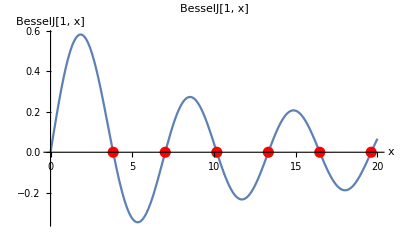

```mathematica
Plot[besselFunction,{x,0,20},PlotRange->All,PlotLabel->"BesselJ[1, x]",AxesLabel->{"x","BesselJ[1, x]"},Epilog->{Red,PointSize[0.02],Point[{#,0}&/@roots]}]
```

first three roots:

```mathematica
roots=x/. NSolve[besselFunction==0&&0<x<12,x]
```

{3.83171,7.01559,10.1735}

Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

```mathematica
f[x_]:= Sin[x]* Exp[-x]
```

```mathematica
D[f[x], x]
```

ⅇ^-x Cos[x]-ⅇ^-x Sin[x]

```mathematica
Integrate[f[x],x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

Q4: Find the series expansion of the function f(x) = e^(-arctan(x)) about x=0, and about x → ∞. Hint: The arctan function is ArcTan[x].

```mathematica
f[x_]:= Exp[-ArcTan[x]]
```

```mathematica
Series[f[x],{x,0,5}]
```

1-x+x^2/2+x^3/6-(7 x^4)/24-x^5/24+O[x]^6

```mathematica
f[x]/.{x->0}
```

1

```mathematica
Series[f[x],{x,∞,5}]
```

ⅇ^(-π/2)+ⅇ^(-π/2)/x+ⅇ^(-π/2)/(2 x^2)-ⅇ^(-π/2)/(6 x^3)-(7 ⅇ^(-π/2))/(24 x^4)+ⅇ^(-π/2)/(24 x^5)+O[1/x]^6

```mathematica
f[x]/.{x->∞}
```

ⅇ^(-π/2)

Q5: Solve the following differential equation using both DSolve and NDSolve (for x=-10 to x=10). Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

```mathematica
DSolve[{y''[x]-x*y[x]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y[x],x]
```

{{y[x]→3^(2/3) AiryAi[x] Gamma[2/3]}}

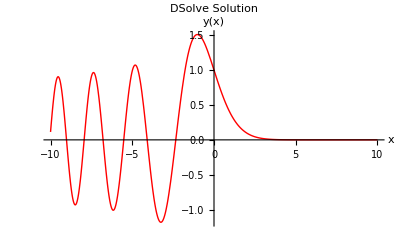

```mathematica
Plot[Evaluate[y[x]/. %],{x,-10,10},PlotStyle->{Red,Thick},PlotLabel->"DSolve Solution",AxesLabel->{"x","y(x)"}]
```

```mathematica
NDSolve[{y''[x]-x*y[x]==0,y[0]==1,y'[0]==-3^(1/3) Gamma[2/3]/Gamma[1/3]},y, {x, -10, 10}]
```

{{y→InterpolatingFunction[…]}}

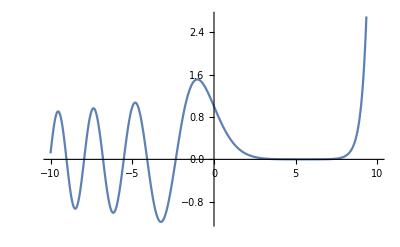

```mathematica
Plot[[x],{x,-10.,10.}]
```

```mathematica
NDSolve[{y''[x]-x*y[x]==0,y[0]==1,y'[0]==-3^(1/3) Gamma[2/3]/Gamma[1/3]},y, {x, -10, 10}];
```

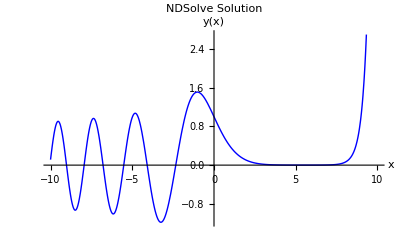

```mathematica
Plot[Evaluate[y[x]/.%],{x,-10,10},PlotStyle->{Blue, Thick},PlotLabel->"NDSolve Solution",AxesLabel->{"x","y(x)"}]
```